```mathematica
a=Exp[I p L/2];
b =Exp[I k L /2];
S={{a, 0, -1/b, -b},{-p a, 0, -k /b, k b},{0, a, -b, -1/b},{0,p a, -k b, k /b}};
v={-1/a,-p /a,0,0};
LinearSolve[S, v]//FullSimplify
```

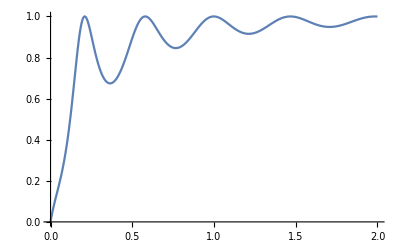

```mathematica
r= 10;
Plot[4u(1+u)/(Sin[2r Sqrt[1+u]]^2+4u(1+u)),{u,0,2},PlotRange->Full]
```

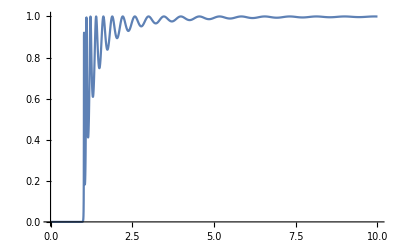

```mathematica
r=10;
Plot[1/(1+Sinh[2 r Sqrt[1-u]]^2/(4u(1-u))),{u,0,10},PlotRange->Full]
```